```mathematica
data=Import["D:\\Documents\\SocialNetwork\\NN\\Kore.txt"];
```

```mathematica
data=StringSplit[data];
```

```mathematica
a=Table[ToExpression[data[[3*i-2]]],{i,1,452}];
b=Table[ToExpression[data[[3*i-1]]],{i,1,452}];
c=Table[ToExpression[data[[3*i]]],{i,1,452}];
```

```mathematica
mat=Table[0,{i,1,44},{j,1,44}];
For[
i=1,
i≤452,
i++,
mat[[a[[i]]]][[b[[i]]]]=1
]
```

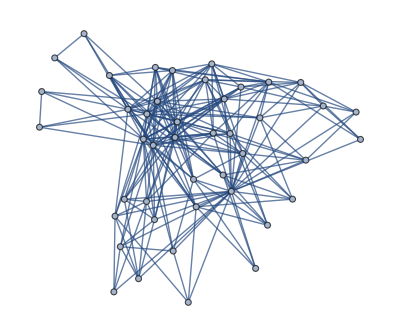

```mathematica
g=AdjacencyGraph[mat]
```

```mathematica
sub=FindGraphCommunities[g,Method->"Modularity"]
```

{{1,3,4,10,12,15,16,17,18,22,23,24,33,34,43},{5,6,27,28,31,32,39,40,41,42},{7,8,9,11,13,14,25,26,35,38},{2,19,20,21,29,30,36,37,44}}

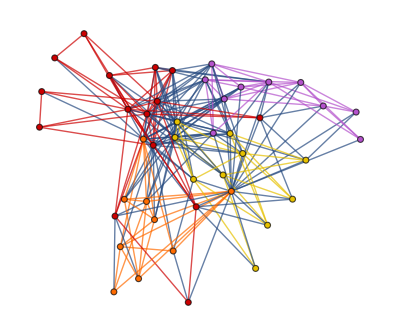

```mathematica
HighlightGraph[g,Map[Subgraph[g,#]&,%]]
```

```mathematica
Length[sub]
```

4

```mathematica
l=VertexDegree[g]
```

{23,22,12,11,17,17,13,13,5,9,7,8,4,9,4,4,4,4,11,9,8,16,18,19,12,11,12,11,6,7,12,10,10,8,10,4,6,12,7,6,6,4,4,27}

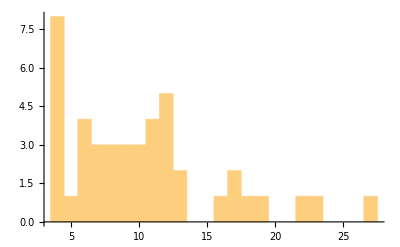

```mathematica
Histogram[l,20]
```

```mathematica
a1=0;
a2=0;
a3=0;
a4=0;
a5=0;
a6=0;
```

```mathematica
aa=VertexDegree[g];
```

```mathematica
For[
i=1,
i≤Length[aa],
i++,
If[
aa[[i]]≥32,
a1++,
{
If[
aa[[i]]≥16,
a2++,
{
If[
aa[[i]]≥8,
a3++,
{
If[
aa[[i]]≥4,
a4++,
{
If[
aa[[i]]≥2,
a5++,
{
If[
aa[[i]]≥1,
a6++
]
}
]
}
]
}
]
}
]
}
]
]
```

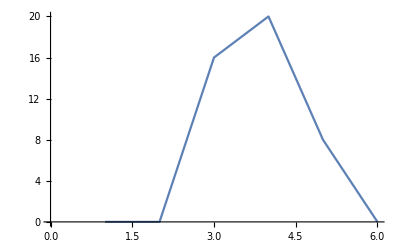

```mathematica
ListPlot[{a6,a5,a4,a3,a2,a1},Joined->True]
```